```mathematica
Quit[];
```

```mathematica
<<Figures`Basic`;
<<Figures`Ticks`;
<<Figures`Color`;
<<Figures`MultiPanel`;
```

```mathematica
Get[NotebookDirectory[]<>"mathematica_package/Basic.m"];
Get[NotebookDirectory[]<>"mathematica_package/Ticks.m"];
Get[NotebookDirectory[]<>"mathematica_package/Color.m"];
Get[NotebookDirectory[]<>"mathematica_package/MultiPanel.m"];
```

## Figure 1: analytical null modes (s=7, σ=1)

plot generated entirely by Mathematica

```mathematica
{s,σ,a}={7,1,1};
(*ρ[ω_]=Exp[-(σ^2 Log[ω/a]^2)/2] Cos[s Log[ω/a]]/(√π(ω/a));*)
ρLog[x_]=Exp[-(σ^2(x-Log[a])^2)/2] Cos[s(x- Log[a])]/(√π(Exp[x]/a));
dx=0.001;
Dl=Table[{k=5*10^-3*Exp[ik/300*Log[4000]],Quiet[1/π Sum[Exp[x]^2/(Exp[x]^2+k^2)ρLog[x]dx,{x,-10,10,dx}]]},{ik,0,300}];
```

```mathematica
βList={1/5,1/2,1,2,5};
Do[
dx=0.001;
Glβ[β]=Table[{τ,1/(2π)Quiet[Sum[Cosh[Exp[x](τ-β/2)]/Sinh[Exp[x] β/2] ρLog[x]Exp[x]dx,{x,-10,10,dx}]]},{τ,0,β,β/100}];
,{β,βList}]
```

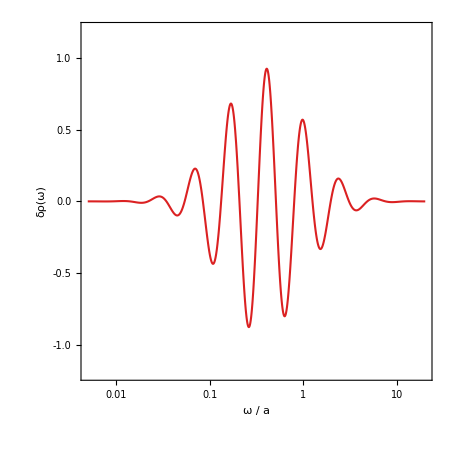

```mathematica
LogLinearPlot[ρLog[Log[ω]],{ω,5*10^-3,20},PlotRange->{{5*10^-3,20},{-1.2,1.2}},FrameLabel->{"ω / a","δρ(ω)"},PlotStyle->Directive[Red,AbsoluteThickness[1.5]]]
```

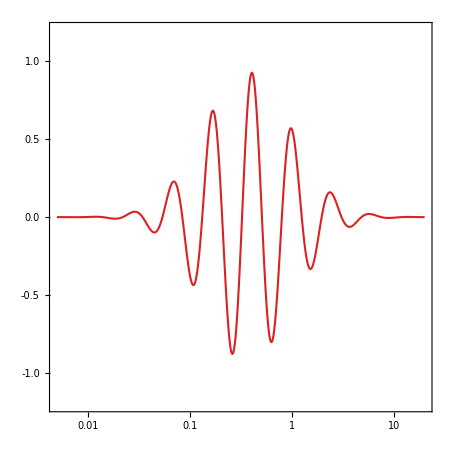

```mathematica
LogLinearPlot[ρLog[Log[ω]],{ω,5*10^-3,20},PlotRange->{{5*10^-3,20},{-1.2,1.2}},FrameLabel->{MaTeX["\\omega / a"],MaTeX["\\delta\\rho(\\omega)"]},PlotStyle->Directive[Red,AbsoluteThickness[1.5]]]
```

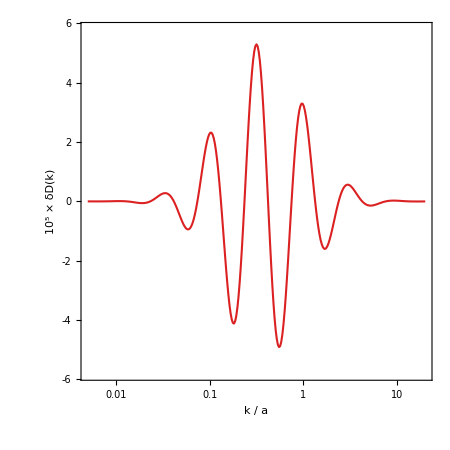

```mathematica
ListLogLinearPlot[Dl.DiagonalMatrix[{1,10^5}],PlotRange->{{5*10^-3,20},{-5.8,5.8}},FrameLabel->{"k / a","10^5 × δD(k)"},Joined->True,PlotStyle->Directive[Red,AbsoluteThickness[1.5]]]
```

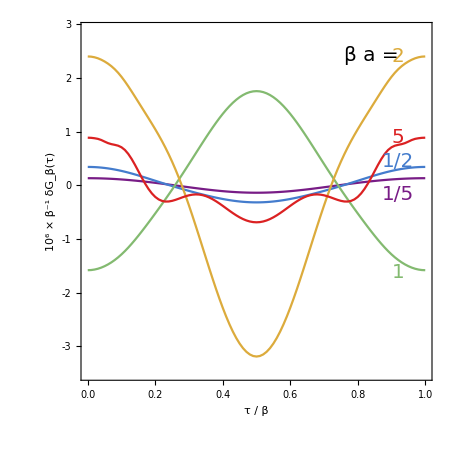

```mathematica
drift={-0.3,0.1,-0.05,0,0.01};
ListPlot[Table[Glβ[ββ].DiagonalMatrix[{1/ββ,10^6/(ββ)^1}],{ββ,βList}],
FrameLabel->{"τ / β","10^6 × β^-1 δG_β(τ)"},Joined->True,PlotRange->{{0,1},{-3.5,2.9}},
PlotStyle->Table[Directive[ColorData["Rainbow",(i-1)/4]],{i,5}],
Epilog->Join[Table[Inset[Style[ToString[InputForm[βList⟦i⟧]],20,FontFamily->"Times",ColorData["Rainbow",(i-1)/4]],{0.92,drift⟦i⟧+10^6/βList⟦i⟧^1 Glβ[βList⟦i⟧]⟦1,2⟧}],{i,5}],
{Inset[Style["β a = ",20,FontFamily->"Times"],{0.84,drift⟦5⟧+10^6/βList⟦4⟧^1 Glβ[βList⟦4⟧]⟦1,2⟧}]}
]
]
```

## Figure B.6: SVD

plot generated entirely by Mathematica

```mathematica
ω=Table[i/25,{i,500}];
k=Table[i/5,{i,100}];
Kmat=Table[N[1/π ω⟦j⟧/(ω⟦j⟧^2+k⟦i⟧^2),18],{i,100},{j,500}];
{u,w,v}=SingularValueDecomposition[Transpose[Kmat]];
λw=Table[w⟦i,i⟧,{i,100}];
```

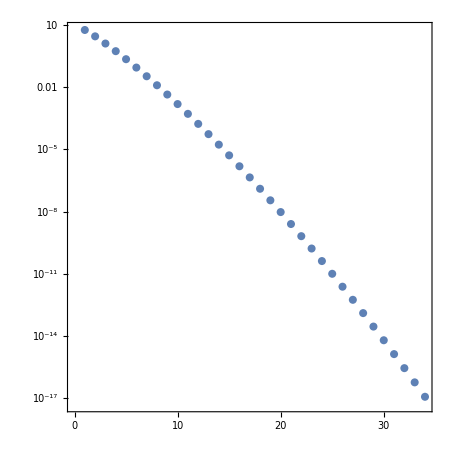

```mathematica
ListLogPlot[λw]
```

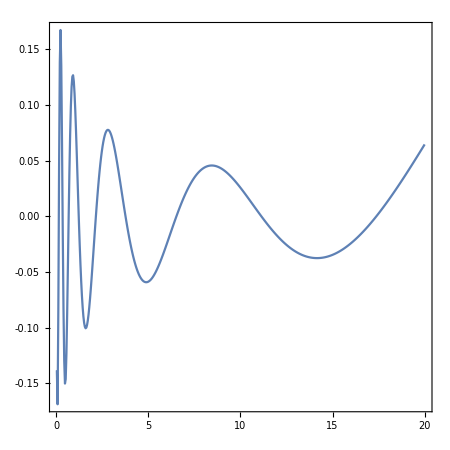

```mathematica
ListPlot[
Transpose[{ω,u⟦;;,10⟧}]
,Joined->True,PlotRange->All]
```

```mathematica
BW[m_,γ_,ω_]:=(4γ ω)/((m^2+γ^2-ω^2)^2+(2γ ω)^2);
ρ=Map[(.8BW[2,0.5,#]+BW[5,0.5,#])&,ω];
```

```mathematica
dmax=-3;Δω=0.2;
```

```mathematica
cut=8;
UTρU=Transpose[u⟦;;,;;cut⟧].DiagonalMatrix[ρ].u⟦;;,;;cut⟧;
m1=Δω*DiagonalMatrix[λw⟦;;cut⟧].UTρU;
data1=Table[{d,1/Min[Abs[Eigenvalues[α d DiagonalMatrix[1/λw⟦;;cut⟧]+m1/d]]]},{α,Table[10^j,{j,-4,4,1}]},{d,Table[10^i,{i,-8,dmax,0.2}]}];
fig1=ListLogLogPlot[
data1,PlotStyle->Table[Directive[AbsoluteThickness[1],ColorData["Rainbow",i/8]],{i,0,8}],FrameLabel->{"d","λ_max"},
PlotRange->{{10^-8,10^-2},{5*10^-5,5*10^3}},Joined->True,Axes->True,
Epilog->Join[{Inset[Style["N_basis",20],{-16,-8.5}],
Inset[Style["8",20],{-16,-6.8}],
Inset[Style["10",20],{-16,-4.8}],
Inset[Style["12",20],{-16,-2.8}],
Inset[Style["α =",20],{-7.1,-2.75}]},Table[Inset[Style["\*SuperscriptBox[10,"<>ToString[i-4]<>"]",20,ColorData["Rainbow",i/8]],Log[data3⟦i+1,-1⟧]+{1.2,0}],{i,0,8}]]
];
```

```mathematica
cut=10;
UTρU=Transpose[u⟦;;,;;cut⟧].DiagonalMatrix[ρ].u⟦;;,;;cut⟧;
m1=Δω*DiagonalMatrix[λw⟦;;cut⟧].UTρU;
data=Table[{d,1/Min[Abs[Eigenvalues[α d DiagonalMatrix[1/λw⟦;;cut⟧]+m1/d]]]},{α,Table[10^j,{j,-4,4,1}]},{d,Table[10^i,{i,-8,dmax,0.2}]}];
fig2=ListLogLogPlot[
data,PlotStyle->Table[Directive[AbsoluteThickness[1],AbsoluteDashing[{10,7}],ColorData["Rainbow",i/8]],{i,0,8}],FrameLabel->{"d","λ_min"},
PlotRange->{{10^-8,20},{2*10^-4,2*10^4}},Joined->True,
Epilog->Join[{Inset[Style["N_basis",20],{-16,9}],
Inset[Style["10",20],{-16,4.5}],
Inset[Style["α =",20],{-.8,7.4}]},Table[Inset[Style["\*SuperscriptBox[10,"<>ToString[i-4]<>"]",20,ColorData["Rainbow",i/8]],Log[data⟦i+1,-1⟧]+{1.2,0}],{i,0,8}]]
];
```

```mathematica
cut=12;
UTρU=Transpose[u⟦;;,;;cut⟧].DiagonalMatrix[ρ].u⟦;;,;;cut⟧;
m1=Δω*DiagonalMatrix[λw⟦;;cut⟧].UTρU;
data3=Table[{d,1/Min[Abs[Eigenvalues[α d DiagonalMatrix[1/λw⟦;;cut⟧]+m1/d]]]},{α,Table[10^j,{j,-4,4,1}]},{d,Table[10^i,{i,-8,dmax,0.2}]}];
fig3=ListLogLogPlot[
data3,PlotStyle->Table[Directive[AbsoluteThickness[2],AbsoluteDashing[{2,7}],ColorData["Rainbow",i/8]],{i,0,8}],FrameLabel->{"d","λ_min"},
PlotRange->{{10^-8,20},{2*10^-4,2*10^4}},Joined->True,
Epilog->Join[{Inset[Style["N_basis",20],{-16,9}],
Inset[Style["12",20],{-16,2.5}],
Inset[Style["α =",20],{-.8,7.4}]},Table[Inset[Style["\*SuperscriptBox[10,"<>ToString[i-4]<>"]",20,ColorData["Rainbow",i/8]],Log[data⟦i+1,-1⟧]+{1.2,0}],{i,0,8}]]
];
```

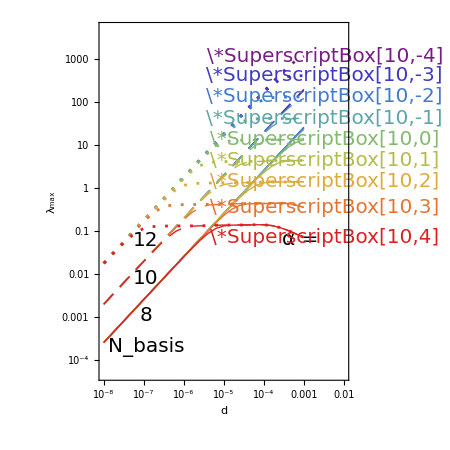

```mathematica
Show[{fig1,fig2,fig3},Axes->True,AxesOrigin->{10,0},AxesStyle->Directive[Black,AbsoluteThickness[1],AbsoluteDashing[{4,5}]]]
```

## Figure 3: check NN solution

files stored "./data/fig3/"; NN results generated by ""; SLSQP result generated by "mem.py";

```mathematica
dir=NotebookDirectory[]<>"data/fig3";
```

### Left: compare solutions

```mathematica
ρIn=Import[dir<>"/True_rho.txt","Data"]⟦;;,{1,2}⟧;
DIn=Import[dir<>"/True_D.txt","Data"]⟦;;,{1,2}⟧;
ρω["true"]=ρIn;
```

```mathematica
Load[tag_]:=Module[{},
ρIn=Import[dir<>"/Rec_rho_"<>tag<>".txt","Data"]⟦;;,{1,2}⟧;
ρω[tag]=ρIn;]
loadlist={"Bryan_L2SP_100_1e-06","NN_d0_1e-06","NN_d1_1e-06","NN_d2_1e-06","NN_d3_1e-06"};
plotlist=Prepend[loadlist,"true"];
Do[Load[x],{x,loadlist}]
PlotStyleList={
Directive[Black,AbsoluteThickness[2]],
Directive[Gray,AbsoluteThickness[3],CapForm["Round"],AbsoluteDashing[{3,9}]],
Directive[Red,AbsoluteThickness[1]],
Directive[Orange,AbsoluteThickness[1]],
Directive[Green,AbsoluteThickness[1]],
Directive[Blue,AbsoluteThickness[1]]
};
```

```mathematica
textlist={"ground truth","SLSQP(l-1=0)","NN, l-1 = 0","NN, l-1 = 1","NN, l-1 = 2","NN, l-1 = 3"};n=Length[textlist];
FigLeg1=ListPlot[Table[{{0,n+0.5-i},{.27,n+0.5-i}},{i,n}],Joined->True,PlotRange->{{0,1},{0,n}},
Epilog->Table[Inset[Style[textlist⟦i⟧,20,FontFamily->"Times New Roman"],{0.3,n+0.5-i},{Left,Center}],{i,n}],
ImageSize->180,Frame->False,ImagePadding->0,AspectRatio->.8,
PlotStyle->PlotStyleList];
```

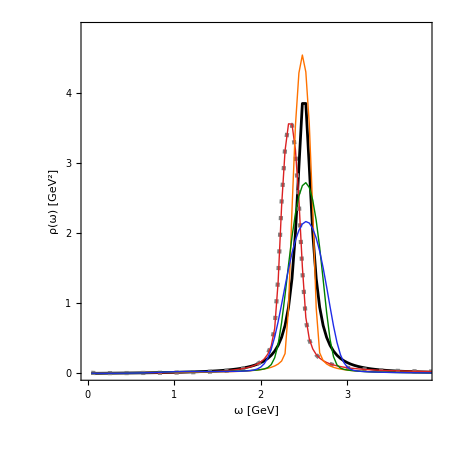

```mathematica
ListPlot[Table[ρω[i],{i,plotlist}],Joined->True,PlotRange->{{0,3.9},{0,4.9}},
FrameLabel->{"ω [GeV]","ρ(ω) [GeV^2]"},PlotStyle->PlotStyleList,Epilog->Inset[FigLeg1,Scaled[{0.3,0.75}]]]
```

### Right: LHS vs RHS

```mathematica
ω=Table[0.04i,{i,500}];
Do[
uniq[i]=Import[dir<>"/test_linear_d"<>ToString[i]<>".txt","Data"];
norm[i]=Total[Log[Exp[Import[dir<>"/rho1_noise0_l21.0E-06_s1.0E-03_w1_d"<>ToString[i]<>".txt","Data"]⟦;;,2⟧]-1]^2];
,{i,0,4}];

PlotStyleList=Map[Directive[#,AbsoluteThickness[1]]&,{Red,Orange,Green,Blue,Purple}];
PlotStyleList2=Map[Directive[#,AbsoluteThickness[3],CapForm["Round"],AbsoluteDashing[{0,7}]]&,{Red,Orange,Green,Blue,Purple}];
textlist={"StyleBox[\"l\",FontSlant->\"Italic\"]StyleBox[\"-\",FontSlant->\"Italic\"]1 = 0","StyleBox[\"l\",FontSlant->\"Italic\"]StyleBox[\"-\",FontSlant->\"Italic\"]1 = 1","StyleBox[\"l\",FontSlant->\"Italic\"]StyleBox[\"-\",FontSlant->\"Italic\"]1 = 2","StyleBox[\"l\",FontSlant->\"Italic\"]StyleBox[\"-\",FontSlant->\"Italic\"]1 = 3"};
n=Length[textlist];
FigLeg2=ListPlot[Table[{{0,n+0.5-i},{.27,n+0.5-i}},{i,n}],Joined->True,PlotRange->{{0,1},{0,n}},
Epilog->Table[Inset[Style[textlist⟦i⟧,20,FontFamily->"Times New Roman"],{0.3,n+0.5-i},{Left,Center}],{i,n}],
ImageSize->150,Frame->False,ImagePadding->0,AspectRatio->0.6,
PlotStyle->PlotStyleList];
```

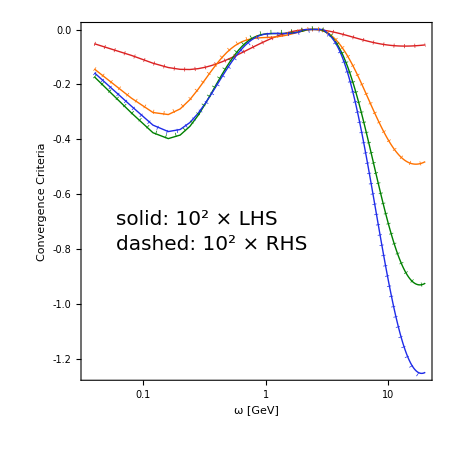

```mathematica
fac=100;
Show[{
ListLogLinearPlot[Table[Transpose[{ω,fac uniq[i]⟦;;,1⟧*norm[i]^(i/(i+1))}],{i,0,3}],Joined->True,PlotRange->All,PlotStyle->PlotStyleList],
ListLogLinearPlot[Table[Transpose[{ω,fac uniq[i]⟦;;,2⟧*norm[i]^(i/(i+1))}],{i,0,3}],Joined->True,PlotRange->All,PlotStyle->PlotStyleList2]
},FrameLabel-> {"ω [GeV]","Convergence Criteria"},Epilog->{
Inset[FigLeg2,Scaled[{0.1,0.2}],{Left,Center}],
Inset[Style["solid: 10^2 × LHS",20,FontFamily->"Times New Roman"],Scaled[{0.1,0.45}],{Left,Center}],
Inset[Style["dashed: 10^2 × RHS",20,FontFamily->"Times New Roman"],Scaled[{0.1,0.38}],{Left,Center}]
}]
```

## Figure 4 and 5: plots in general coordinate and momentum spaces

files stored "./data/fig4/"  and "./data/fig5/"; NN results generated by ""; NN-P2P results generated by ""; MEM result generated by "mem.py";

### Settings

```mathematica
Coef["BW","Lehmann","+",s_,v_,ϕ_]:=√π Sinh[(π s)/2-ϕ s]/Sinh[(π s)/2] Cos[s v]/(Exp[v]Cos[ϕ]);
Coef["BW","Lehmann","-",s_,v_,ϕ_]:=√π Sinh[(π s)/2-ϕ s]/Sinh[(π s)/2] Sin[s v]/(Exp[v]Cos[ϕ]);
λ[s_]:=1/(2Cosh[π s/2]);
γ=0.5;m1=2;m2=5;
v1=Log[m1^2+γ^2]/2;
ϕ1=ArcTan[m1,γ];
v2=Log[m2^2+γ^2]/2;
ϕ2=ArcTan[m2,γ];
```

```mathematica
dir=NotebookDirectory[]<>"data/fig4";
ρIn=Import[dir<>"/True_rho.txt","Data"]⟦;;,{1,2}⟧;
DIn=Import[dir<>"/True_D.txt","Data"]⟦;;,{1,2}⟧;
ρDsIn=Import[dir<>"/True_rho_D_s.txt","Data"];
ω=ρIn⟦;;,1⟧;
s=ρDsIn⟦;;,1⟧;
ρsCos["ana"]=Map[{#,(0.8Coef["BW","Lehmann","+",#,v1,ϕ1]+1.0Coef["BW","Lehmann","+",#,v2,ϕ2])}&,s];
ρsSin["ana"]=Map[{#,(0.8Coef["BW","Lehmann","-",#,v1,ϕ1]+1.0Coef["BW","Lehmann","-",#,v2,ϕ2])}&,s];
DsCos["ana"]=Transpose[{s,ρsCos["ana"]⟦;;,2⟧ λ[s]}];
DsSin["ana"]=Transpose[{s,ρsSin["ana"]⟦;;,2⟧ λ[s]}];
tag="true";
ρω[tag]=ρIn;
Dk[tag]=DIn;
ρsCos[tag]=Transpose[{s,ρDsIn⟦;;,2⟧}];
ρsSin[tag]=Transpose[{s,ρDsIn⟦;;,3⟧}];
DsCos[tag]=Transpose[{s,ρDsIn⟦;;,4⟧}];
DsSin[tag]=Transpose[{s,ρDsIn⟦;;,5⟧}];
```

```mathematica
Load[tag_]:=Module[{},
ρIn=Import[dir<>"/Rec_rho_"<>tag<>".txt","Data"]⟦;;,{1,2}⟧;
DIn=Import[dir<>"/Rec_D_"<>tag<>".txt","Data"]⟦;;,{1,2}⟧;
ρDsIn=Import[dir<>"/Rec_rho_D_s_"<>tag<>".txt","Data"];
ρω[tag]=ρIn;
Dk[tag]=DIn;
ρsCos[tag]=Transpose[{s,ρDsIn⟦;;,2⟧}];
ρsSin[tag]=Transpose[{s,ρDsIn⟦;;,3⟧}];
DsCos[tag]=Transpose[{s,ρDsIn⟦;;,4⟧}];
DsSin[tag]=Transpose[{s,ρDsIn⟦;;,5⟧}];]
```

```mathematica
smin=0.1;ωmin=0.2;scut=3;
AuxStyle=Directive[Black,AbsoluteThickness[1],AbsoluteDashing[{2,7}]];
FigAux=ListLogLinearPlot[{{{smin,0},{29,0}},{{scut,-2},{scut,2}}},Joined->True,PlotStyle->AuxStyle];
```

### Figure 4: noise=0

```mathematica
dir=NotebookDirectory[]<>"data/fig4";
loadlist={"Bryan_SJ_100_Int","Bryan_SJ_8_Int","NNP2P","NN"};
plotlist=Prepend[loadlist,"true"];
splotlist=Join[{"ana"},plotlist];
Do[Load[x],{x,loadlist}]
Do[
DsCosProj[x]=Transpose[{s,ρsCos[x]⟦;;,2⟧λ[s]}];
DsSinProj[x]=Transpose[{s,ρsSin[x]⟦;;,2⟧λ[s]}];
,{x,plotlist}];
len=Length[plotlist]-2;
PlotStyleList=Join[{
Directive[Black,AbsoluteThickness[1.5]]},
Map[Directive[#,AbsoluteThickness[1.5]]&,{Orange,Green,Blue,Red}]
];
```

```mathematica
textlist={"ground truth","MEM,N_basis=100","MEM,N_basis=8","NN-P2P","NN"};
FigLeg2=ListPlot[Table[{{0,5.5-i},{.27,5.5-i}},{i,5}],Joined->True,PlotRange->{{0,1.5},{0,5}},
Epilog->Table[Inset[Style[textlist⟦i⟧,20,FontFamily->"Times New Roman"],{0.3,5.5-i},{Left,Center}],{i,5}],
ImageSize->180,Frame->False,ImagePadding->0,AspectRatio->.8,
PlotStyle->PlotStyleList];
```

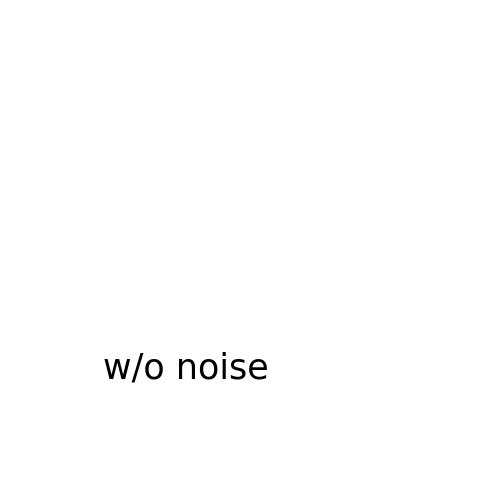

-Graphics-

-Graphics-

```mathematica
smin=0.1;ωmin=0.2;scut=3;
FigDsin=Show[{ListLogLinearPlot[Table[DsSin[i],{i,plotlist}],
Joined->True,PlotRange->{{smin,29},{-0.02,0.19}},
FrameLabel->{"s","(D̃)_-(s)[GeV^2]  "},
PlotStyle->PlotStyleList,FrameTicks->{{LinearTicks[-0.1,.5,True]&,LinearTicks[-0.1,.5,False]&},{LogTicks[#1,#2,True]&,LogTicks[#1,#2,False]&}}],FigAux}];
FigDcos=Show[{ListLogLinearPlot[Table[DsCos[i],{i,plotlist}],
Joined->True,PlotRange->{{smin,29},{-0.05,0.49}},
FrameLabel->{"s","(D̃)_+(s)[GeV^2]  "},
PlotStyle->PlotStyleList,FrameTicks->{{LinearTicks[-0.2,0.6,True]&,LinearTicks[-0.2,0.6,False]&},{LogTicks[#1,#2,True]&,LogTicks[#1,#2,False]&}}],
FigAux}];
Figρcos=Show[{ListLogLinearPlot[Table[ρsCos[i],{i,plotlist}],
Joined->True,PlotRange->{{smin,29},{-0.39,0.99}},
FrameLabel->{"s","(ρ̃)_+(s) [GeV^2]"},
PlotStyle->PlotStyleList],FigAux}];
Figρsin=Show[{ListLogLinearPlot[Table[ρsSin[i],{i,plotlist}],
Joined->True,PlotRange->{{smin,29},{-0.39,0.79}},
FrameLabel->{"s","(ρ̃)_-(s) [GeV^2]"},
PlotStyle->PlotStyleList],FigAux}];
Figρ=ListLogLinearPlot[Table[ρω[i],{i,plotlist}],Joined->True,PlotRange->{{ωmin,20},{-0.05,0.9}},FrameLabel->{"ω, k [GeV]","ρ(ω) [GeV^2]"},PlotStyle->PlotStyleList];
FigD=ListLogLinearPlot[Table[Dk[i],{i,plotlist}],Joined->True,PlotRange->{{ωmin,20},{0,.24}},FrameLabel->{"ω, k [GeV]","D(k) [GeV^2] "},PlotStyle->PlotStyleList,FrameTicks->{{LinearTicks[0,.5,True]&,LinearTicks[0,.5,False]&},{LogTicks[#1,#2,True]&,LogTicks[#1,#2,False]&}}];
figcor=MultiPanel[{Figρ,FigD},yRatios->{7,3},
Epilog->{Inset[Style["w/o noise",35],Scaled[{0.35,0.22}]],
Inset[FigLeg2,Scaled[{0.36,0.78}]]}]
figcos=MultiPanel[{Figρcos,FigDcos},yRatios->{7,3}]
figsin=MultiPanel[{Figρsin,FigDsin},yRatios->{7,3}]
Export[NotebookDirectory[]<>"compare_real_0.pdf",figcor];
Export[NotebookDirectory[]<>"compare_eigen_cos_0.pdf",figcos];
Export[NotebookDirectory[]<>"compare_eigen_sin_0.pdf",figsin];
```

### Figure 5: noise=10^-4

```mathematica
dir=NotebookDirectory[]<>"data/fig5";
loadlist={"Bryan_SJ_100_Int","Bryan_SJ_8_Int","NNP2P","NN"};
plotlist=Prepend[loadlist,"true"];
splotlist=Join[{"ana"},plotlist];
Do[Load[x],{x,loadlist}]
Do[
DsCosProj[x]=Transpose[{s,ρsCos[x]⟦;;,2⟧λ[s]}];
DsSinProj[x]=Transpose[{s,ρsSin[x]⟦;;,2⟧λ[s]}];
,{x,plotlist}];
len=Length[plotlist]-2;
PlotStyleList=Join[{
Directive[Black,AbsoluteThickness[1.5]]},
Map[Directive[#,AbsoluteThickness[1.5]]&,{Orange,Green,Blue,Red}]
];
```

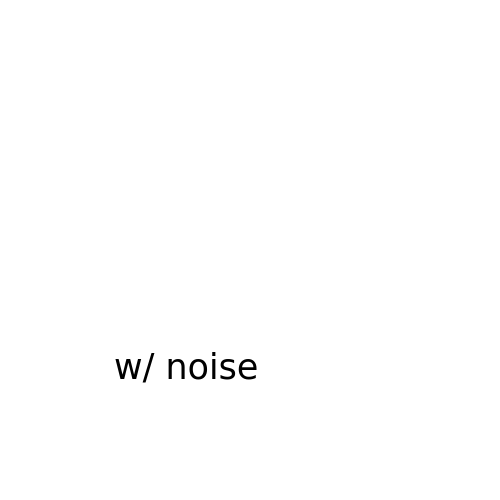

-Graphics-

-Graphics-

```mathematica
smin=0.1;ωmin=0.2;scut=3;
FigDsin=Show[{ListLogLinearPlot[Table[DsSin[i],{i,plotlist}],
Joined->True,PlotRange->{{smin,29},{-0.02,0.19}},
FrameLabel->{"s","(D̃)_-(s)[GeV^2]  "},
PlotStyle->PlotStyleList,FrameTicks->{{LinearTicks[-0.1,.5,True]&,LinearTicks[-0.1,.5,False]&},{LogTicks[#1,#2,True]&,LogTicks[#1,#2,False]&}}],FigAux}];
FigDcos=Show[{ListLogLinearPlot[Table[DsCos[i],{i,plotlist}],
Joined->True,PlotRange->{{smin,29},{-0.05,0.49}},
FrameLabel->{"s","(D̃)_+(s)[GeV^2]  "},
PlotStyle->PlotStyleList,FrameTicks->{{LinearTicks[-0.2,0.6,True]&,LinearTicks[-0.2,0.6,False]&},{LogTicks[#1,#2,True]&,LogTicks[#1,#2,False]&}}],
FigAux}];
Figρcos=Show[{ListLogLinearPlot[Table[ρsCos[i],{i,plotlist}],
Joined->True,PlotRange->{{smin,29},{-0.39,0.99}},
FrameLabel->{"s","(ρ̃)_+(s) [GeV^2]"},
PlotStyle->PlotStyleList],FigAux}];
Figρsin=Show[{ListLogLinearPlot[Table[ρsSin[i],{i,plotlist}],
Joined->True,PlotRange->{{smin,29},{-0.39,0.79}},
FrameLabel->{"s","(ρ̃)_-(s) [GeV^2]"},
PlotStyle->PlotStyleList],FigAux}];
Figρ=ListLogLinearPlot[Table[ρω[i],{i,plotlist}],Joined->True,PlotRange->{{ωmin,20},{-0.05,0.9}},FrameLabel->{"ω, k [GeV]","ρ(ω) [GeV^2]"},PlotStyle->PlotStyleList];
FigD=ListLogLinearPlot[Table[Dk[i],{i,plotlist}],Joined->True,PlotRange->{{ωmin,20},{0,.24}},FrameLabel->{"ω, k [GeV]","D(k) [GeV^2] "},PlotStyle->PlotStyleList,FrameTicks->{{LinearTicks[0,.5,True]&,LinearTicks[0,.5,False]&},{LogTicks[#1,#2,True]&,LogTicks[#1,#2,False]&}}];
figcor=MultiPanel[{Figρ,FigD},yRatios->{7,3},Epilog->{Inset[Style["w/ noise",35],Scaled[{0.35,0.22}]]}]
figcos=MultiPanel[{Figρcos,FigDcos},yRatios->{7,3}]
figsin=MultiPanel[{Figρsin,FigDsin},yRatios->{7,3}]
Export[NotebookDirectory[]<>"compare_real_1.pdf",figcor];
Export[NotebookDirectory[]<>"compare_eigen_cos_1.pdf",figcos];
Export[NotebookDirectory[]<>"compare_eigen_sin_1.pdf",figsin];
```